```mathematica
<<Teukolsky`
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
```

# Asymptotic scalar field equations

## r_out

```mathematica
Initψout[l_,m_,kout_,a_,M_,r0_] := 
Module[{i = l, j= m , N=kout, s = a, Μ=M, ρ0 = r0,f0,f1,f2,f3,f4,f5,f6,n,ω,rp,rm,λ,Q = SpinWeightedSpheroidalEigenvalue},
rp= Μ+√(Μ^2-s^2);
rm = Μ-√(Μ^2-s^2);
ω = j/Μ(Μ/ρ0)^(3/2)/(1+(s/Μ)(Μ/ρ0)^(3/2));
f0= -2 ⅈ n ω;
f1=n^2-λ+ω (-4 ⅈ Μ+s^2 ω)+n (-1+4 ⅈ Μ ω);
f2=-2 ⅈ s^2 (-2+n) ω+2Μ (-3+5 n-2 n^2+λ-2 s j ω+s^2 ω^2);
f3=4 Μ^2 (-2+n)^2+s^2 (8+j^2-8 n+2 n^2-λ);
f4=-2 a^2 Μ (15-11 n+2 n^2);
f5=s^4 (12-7 n+n^2);
λ = Q[0,i,j,s ω];
cs = RecurrenceTable[{f0 c[n]+f1 c[n-1]+f2 c[n-2]+f3 c[n-3]+f4 c[n-4]+f5 c[n-5]==0,c[1]==1,c[0]==0,c[-1]==0,c[-2]==0,c[-3]==0},c,{n,1,N}]
]
ψout[l_,m_,kout_,a_,M_,r0_,r_,c_]:=Exp[ⅈ m/M 1/((r0/M)^(3/2)+a/M) (r+M Log[(r^2-2 M r +a^2)/M^2]+(2 M^2-a^2)/(2 √(M^2-a^2))Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))])]Sum[c[[n]] r^-n,{n,1,kout}]
```

```mathematica
l=1;
m=1;
M=1`32;
a =  0.998`32M;
r0 = 10`32M;
ω = m/M 1/((r0/M)^(3/2)+a/M);
```

```mathematica
X = Initψout[l,m,1000,a,M,r0];
f[r_]:= Quiet[ψout[l,m,1000,a,M,r0,r,X]];
R = TeukolskyRadial[0,l,m,a,ω]["Up"];
```

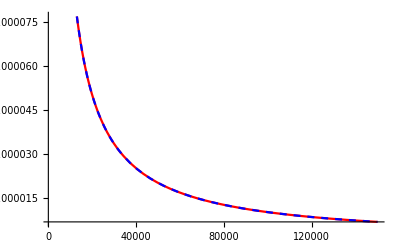

```mathematica
Plot[{Abs[f[r]],Abs[R[r]]},{r,1000,150000},PlotStyle->{Red,{Dashed,Blue}}]
```

```mathematica
9
```

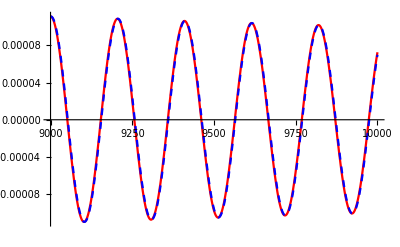

```mathematica
Plot[{Re[f[r]],Re[R[r]]},{r,9000,10000},PlotStyle->{Red,{Dashed,Blue}}]
```

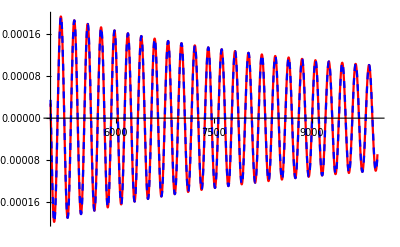

```mathematica
Plot[{Im[f[r]],Im[R[r]]},{r,5000,10000},PlotStyle->{Red,{Dashed,Blue}}]
```

## r_in

```mathematica
Initψin[i_,j_,kin_,α_,Μ_,ρ0_] := 
Module[{l = i, m= j , N=kin, a = α, M=Μ, r0 = ρ0,f,k,ω,γ,rp,rm,λ,Q = SpinWeightedSpheroidalEigenvalue,f0,f1,f2,f3,f4,f5,f6,c},
rp= M+√(M^2-a^2);
rm = M-√(M^2-a^2);
ω = m/M 1/((r0/M)^(3/2)+a/M);
γ = (2M rp ω-a m)/rp^2;

λ = Q[0,l,m,a ω];
f0 = a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2)));
f1 = 2 (-6 a m M rp^2 ω+a^2 (rp (2+4 (-1+k)^2+m^2+(-1+k) (-7-6 ⅈ rp γ)-λ+2 rp^2 ω^2)+M (-3+5 (-1+k)-2 (-1+k)^2+3 rp^2 ω^2))+rp (2 (2-7 (-1+k)+4 (-1+k)^2) M^2+M rp (-3+26 (-1+k)-20 (-1+k)^2+20 ⅈ (-1+k) rp γ+3 λ)-rp^2 (-10 (-1+k)^2+5 (-1+k) (2+3 ⅈ rp γ)+2 λ+3 rp^2 (γ^2-ω^2))));
f2 = 4 (-3+k)^2 M^2+2 M rp (-3+14 (-2+k)-10 (-2+k)^2+20 ⅈ (-2+k) rp γ+3 λ)-12 a m M rp ω+a^2 (2+2 (-2+k)^2+m^2+(-2+k) (-4-8 ⅈ rp γ)-λ+6 M rp ω^2+6 rp^2 ω^2)-rp^2 (-15 (-2+k)^2+5 (-2+k) (3+8 ⅈ rp γ)+6 λ+15 rp^2 (γ^2-ω^2));
f3 = 6 (-3+k)^2 rp-2 ⅈ (-3+k) (-3 ⅈ rp+a^2 γ+15 rp^2 γ)+2 M (-1-2 (-3+k)^2+(-3+k) (3+10 ⅈ rp γ)+λ-2 a m ω+a^2 ω^2)+4 rp (-λ+a^2 ω^2-5 rp^2 (γ^2-ω^2));
f4 = (-4+k)^2+ⅈ (-4+k) (ⅈ+4 M γ-12 rp γ)-λ+a^2 ω^2-15 rp^2 (γ^2-ω^2);
f5 = -2 ⅈ (-5+k) γ+6 rp (-γ^2+ω^2);
f6 = -γ^2+ω^2;

cs = RecurrenceTable[{c[k] f0+c[-1+k] f1+c[-2+k] f2+c[-3+k] f3+c[-4+k] f4+c[-5+k] f5+c[-6+k] f6==0,c[0]==1,c[-1]==0,c[-2]==0,c[-3]==0,c[-4]==0,c[-5]==0},c,{k,0,N}]
]
ψin[l_,m_,kin_,a_,M_,r0_,r_,c_]:=Module[
{i=l,j=m,N=kin,α=a,Μ=M,ρ0=r0,ρ=r,C=c,ω,γ,rp,rm,rs},
ω = j/Μ 1/((ρ0/Μ)^(3/2)+α/Μ);
rp = Μ+√(Μ^2-α^2);
rm = Μ-√(Μ^2-α^2);
γ = (2Μ rp ω -α j)/rp^2;
rs = ρ + Μ Log[((ρ-rp)(ρ-rm))/Μ^2]+(2 Μ^2-α^2)/(2 √(Μ^2-α^2))Log[(ρ-rp)/(ρ-rm)];
Exp[-ⅈ γ rs]Sum[C[[n+1]](ρ-rp)^n,{n,0,N}]
]
```

```mathematica
X = Initψin[l,m,1000,a,M,r0];
f[r_]:= Quiet[ψin[l,m,1000,a,M,r0,r,X]];
R = TeukolskyRadial[0,l,m,a,ω]["In"];
X[[1;;4]]
```

{1.,1.0432772893083605053744-15.39507921560261598727623 ⅈ,-117.847503202517327407307+37.5442565786096426900707 ⅈ,702.176660736258767956697+372.013483231954803135248 ⅈ}

```mathematica
(.84+ⅈ.55){1.`28.90431986523364,1.0432772893083605053744036271875084742`24.399792729926304-15.39507921560261598727623107725886417451`25.828220830384442 ⅈ,-117.84750320251732740730699806747030186029`25.202035039793156+37.54425657860964269007073801741725024242`24.66419690884291 ⅈ,702.17666073625876795669665666417022662625`24.74541297998381+372.01348323195480313524805370635825729982`24.437977975361683 ⅈ}
```

{0.84+0.55 ⅈ,9.34365-12.3581 ⅈ,-119.641-33.279 ⅈ,385.221+698.688 ⅈ}

```mathematica
{0.84+0.55 ⅈ,9.343646491600506-12.358064031986403 ⅈ,-119.64124380834885-33.27895123535051 ⅈ,385.220979240895+698.6884893197579 ⅈ}
```

{0.84+0.55 ⅈ,9.34365-12.3581 ⅈ,-119.641-33.279 ⅈ,385.221+698.688 ⅈ}

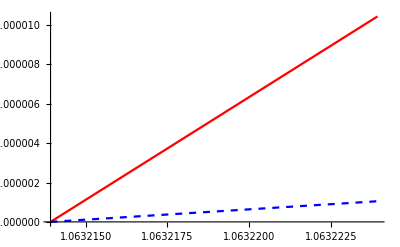

```mathematica
Plot[{Abs[f[r]],Abs[R[r]]},{r,M+√(M^2-a^2),M+√(M^2-a^2)+.00001},PlotStyle->{Red,{Dashed,Blue}}]
```

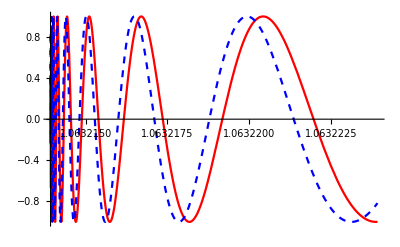

```mathematica
Plot[{Re[f[r]],Re[R[r]]},{r,M+√(M^2-a^2),M+√(M^2-a^2)+.00001},PlotStyle->{Red,{Dashed,Blue}}]
```

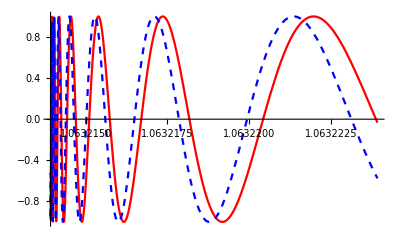

```mathematica
Plot[{Im[f[r]],Im[R[r]]},{r,M+√(M^2-a^2),M+√(M^2-a^2)+.00001},PlotStyle->{Red,{Dashed,Blue}}]
```

```mathematica
γ =(2 M (M+√(M^2-a^2))ω - a m)/((M+√(M^2-a^2))^2);
```

```mathematica
Plot[{Re[Exp[ⅈ γ (r + M Log[((r-M-√(M^2-a^2))(r-M+√(M^2-a^2)))/M^2]+(2 M^2-a^2)/(2(M^2-a^2)^(1/2))Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))])]R[r]],Im[Exp[ⅈ γ (r + M Log[((r-M-√(M^2-a^2))(r-M+√(M^2-a^2)))/M^2]+(2 M^2-a^2)/(2(M^2-a^2)^(1/2))Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))])]R[r]]},{r,M+√(M^2-a^2),M+√(M^2-a^2)+1},PlotLabels->{"Re","Im"},PlotStyle->{Red,Blue}]
```

-Graphics-

```mathematica
√((.84)^2+(.55)^2)
```

1.00404

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^67 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

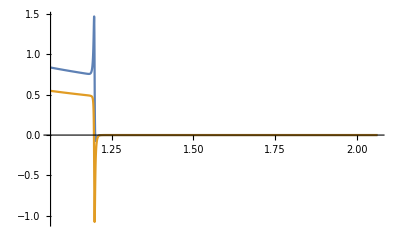

```mathematica
Plot[{Re[R[r]/f[r]],Im[R[r]/f[r]]},{r,M+√(M^2-a^2),M+√(M^2-a^2)+1},PlotRange->All]
```